# Allan Variance for DNA Sequence

## 準備

```mathematica
Get["/home/kamano/SCRIPT-MATHEMATICA/SCRIPTS/DNA_sequence_operations.txt"]
```

## Allan Variance Plot 手順

ベクトル a = {a1,a2,a3...}とする。

時間幅(window の大きさ)wを決定する

ベクトルa より、幅wからなるすべてのサブリストを生成する

すべての隣接するサブリスト(window) 間の平均差をとる

その平均差の値を2 乗したものの平均に、1/2 を掛けた値がAllan Variance と
なる

上記1-4 のステップを、可能なwにつき行う

wを横軸座標に、対応するAllan Variance のルートを縦軸座標に、両対数プロッ
トしたものがAllan Variance Plot である

アランバリアンスの式 :

```mathematica
allanVar[ylist_,w_]:=1/2 Mean[(ListCorrelate[Append[PadRight[{-1},w],1],MovingAverage[ylist,w]])^2]
```

### Plot example (from Wolfram MathSource)

```mathematica
Manipulate[
Module[{Ntot,opts,ylist,g1,g2,Npts,τdata,σdata,στdata},
Ntot=5000;
opts=Sequence[Frame->True,Axes->False,Joined->True,GridLines->Automatic,BaseStyle->12,ImageSize->480];
ylist=RandomReal[NormalDistribution[0,a],Ntot]+b Cos[(2 π)/T Range[Ntot]]+d Range[Ntot];
g1=ListPlot[ylist,FrameLabel->{"t [s]","y(t)"},PlotRange->{All,{-0.4,0.4}},AspectRatio->0.17,opts];
Npts=30;
τdata=Union[ Table[Round[10^((i-1)Log[10,1000]/Npts)],{i,1,Npts+1}]];
σdata=√allanVar[ylist,#]& /@ τdata;
στdata=Transpose[{τdata,σdata}];
g2=Show[
ListLogLogPlot[στdata,PlotMarkers->Automatic,FrameLabel->{"τ [s]","σ_y(τ)"},PlotRange->{All,{0.00009,0.2}},AspectRatio->0.48,opts,FrameTicks->{{1,10,100,1000},{{10^-4,"10^-4"},{10^-3,"10^-3"},{10^-2,"10^-2"},{10^-1,"10^-1"}},None,None}],
LogLogPlot[b Sin[π τ /T]^2/ (π τ/T),{τ,1,1000},PlotStyle->Directive[{Thick,Dashed,RGBColor[.49,0,0]}]],
LogLogPlot[d τ/√2,{τ,1,1000},PlotStyle->Directive[{Thick,Dashed,Darker@RGBColor[.6,.73,.36]}]]
];
Column[{g1,g2}]
],
{{a,0.05,"white frequency noise amplitude"},0.01,0.1,Appearance->"Labeled"},
{{b,0.012,"oscillation amplitude"},0,0.1,Appearance->"Labeled"},
{{T,100,"oscillation period (s)"},10,1000,Appearance->"Labeled"},
{{d,0.000005,"drift (1/s)"},0,0.0001,Appearance->"Labeled"},
SaveDefinitions->True,TrackedSymbols:>{a,b,T,d}
]
```

## Allan Variance Plot DNA塩基配列への応用手順：オリゴヌクレオチド法

DNA 塩基配列データを、a = {a1,a2,a3...}とする(a1、a2... は、塩基)。

部分塩基配列(window) の大きさw 決定する

全塩基配列データa より、幅w からなるすべての部分塩基配列を生成する

すべての隣接する部分塩基配列(window) 間の距離をとる

オリゴヌクレオチド頻度ベクトルを生成し、ベクトルはノルム1にノーマライズする(NEW)

距離はオリゴヌクレオチド頻度ベクトルにおけるユークリッド距離とする

オリゴヌクレオチド頻度は部分配列において取りうるすべてのオリゴヌク
レオチド長n を考える

その距離を2 乗したものの平均に、1/2 を掛けた値がAllan Variance 様値となる

上記1-4 のステップを、可能なw、n につき行う

各nにつき、w を横軸座標に、対応するAllan Variance 様値のルートを縦軸座
標に、両対数プロットしたものがAllan Variance 様Plot となる

アランバリアンス様値の式 :

DNAシークエンスを用意

```mathematica
dnaseq="AAGTTTCGGGGCATTTTGCCCCA"
```

AAGTTTCGGGGCATTTTGCCCCA

1. 部分塩基配列 (window) の大きさw 決定する (w=7)

2. 全塩基配列データa より、幅w からなるすべての部分塩基配列を生成する

```mathematica
dnasubseqs=seqToSubseqs[dnaseq,7]
```

{AAGTTTC,AGTTTCG,GTTTCGG,TTTCGGG,TTCGGGG,TCGGGGC,CGGGGCA,GGGGCAT,GGGCATT,GGCATTT,GCATTTT,CATTTTG,ATTTTGC,TTTTGCC,TTTGCCC,TTGCCCC,TGCCCCA}

3.1. すべての隣接配列のペアを生成

```mathematica
contactPair[dnasubseqs,7]
```

{{AAGTTTC,GGGGCAT},{AGTTTCG,GGGCATT},{GTTTCGG,GGCATTT},{TTTCGGG,GCATTTT},{TTCGGGG,CATTTTG},{TCGGGGC,ATTTTGC},{CGGGGCA,TTTTGCC},{GGGGCAT,TTTGCCC},{GGGCATT,TTGCCCC},{GGCATTT,TGCCCCA}}

1 - 3. wを決定(w=7) - すべての部分配列を生成(seqToSubseqs) - nを決定(n=3) - 部分配列をベクトルに変換(oligonucToVec) - すべての隣接ベクトルのペアを生成(contactPair)

```mathematica
(cpvec[7,3]=contactPair[Map[Normalize[oligonucToVec[#,3]]&,seqToSubseqs[dnaseq,7]],7])//Dimensions
```

{10,2,64}

4. その距離を2 乗したものの平均に、1/2 を掛けた値がAllan Variance 様値となる

```mathematica
AllanDNA[7,3]=Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,cpvec[7,3]//N]]/2
```

0.946194

1 - 4. を一気に行う

```mathematica
AllanDNA[7,1]=Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,1]]&,seqToSubseqs[dnaseq,7]],7]//N]]/2
```

0.341362

```mathematica
AllanDNA[7,2]=Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,2]]&,seqToSubseqs[dnaseq,7]],7]//N]]/2
```

0.766108

```mathematica
AllanDNA[7,3]=Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,3]]&,seqToSubseqs[dnaseq,7]],7]//N]]/2
```

0.946194

## Allan Variance Plot DNA塩基配列への応用例

### PolyA

```mathematica
testSeqPolyA=StringJoin[Table["A",{500}]];
```

```mathematica
AbsoluteTiming[AllanDNA["A",100,5]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyA,w]],w]//N]]/2,{w,10,100,10},{n,1,5}]]]
```

{8.34493,{{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}}

### PolyACGT

```mathematica
testSeqPolyACGT=StringJoin[Table["ACGT",{500}]];
```

長さ500*4のシークエンス
w: 4から16
n: 1から4

```mathematica
AbsoluteTiming[AllanDNA["ACGT",4,16,1,4]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,4,16,1},{n,1,4}]]]
```

{11.93755,{{0.,0.,0.,0.},{0.142857,0.,0.333333,0.5},{0.2,0.142857,0.,0.333333},{0.0769231,0.1,0.142857,0.},{0.,0.,0.,0.},{0.047619,0.,0.0769231,0.1},{0.0769231,0.047619,0.,0.0769231},{0.0322581,0.0384615,0.047619,0.},{0.,0.,0.,0.},{0.0232558,0.,0.0322581,0.0384615},{0.04,0.0232558,0.,0.0322581},{0.0175439,0.02,0.0232558,0.},{0.,0.,0.,0.}}}

```mathematica
AllanDNA["ACGT",4,16,1,4]//TableForm
```

0. | 0. | 0. | 0.
0.142857 | 0. | 0.333333 | 0.5
0.2 | 0.142857 | 0. | 0.333333
0.0769231 | 0.1 | 0.142857 | 0.
0. | 0. | 0. | 0.
0.047619 | 0. | 0.0769231 | 0.1
0.0769231 | 0.047619 | 0. | 0.0769231
0.0322581 | 0.0384615 | 0.047619 | 0.
0. | 0. | 0. | 0.
0.0232558 | 0. | 0.0322581 | 0.0384615
0.04 | 0.0232558 | 0. | 0.0322581
0.0175439 | 0.02 | 0.0232558 | 0.
0. | 0. | 0. | 0.

```mathematica
ListPlot3D[AllanDNA["ACGT",4,16,1,4]]
```

-Graphics3D-

```mathematica
AbsoluteTiming[AllanDNA["ACGT",5,16,5,5]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,5,16},{n,5,5}]]]
```

{25.07233,{{1.},{1.},{0.333333},{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.}}}

```mathematica
AbsoluteTiming[AllanDNA["ACGT",4,16,1,1]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,4,16,1},{n,1,1}]]]
```

{0.85429,{{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.},{0.0232558},{0.04},{0.0175439},{0.}}}

```mathematica
AllanDNA["ACGT",4,16,1,1]
```

{{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.},{0.0232558},{0.04},{0.0175439},{0.}}

### Random

```mathematica
(testseqRandom=StringJoin[Table[RandomInteger[{1,4}],{4000}]/.{1->"A",2->"C",3->"G",4->"T"}])//StringLength
```

4000

長さ4000のシークエンス
w: 2,3
n: 1から3

```mathematica
AbsoluteTiming[AllanDNA["Random",2,3,1,2]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testseqRandom,w]],w]//N]]/2,{w,2,3},{n,1,2}]]]
```

{1.39166,{{0.578158,0.941706},{0.464858,0.875566}}}

```mathematica
AbsoluteTiming[AllanDNA["Random",3,3,3,3]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testseqRandom,w]],w]//N]]/2,{w,3,3},{n,3,3}]]]
```

{1.02175,{{0.979975}}}

```mathematica
AllanDNA["Random",2,3,1,3]=Map[PadRight[#,4]&,Insert[AllanDNA["Random",2,3,1,2],AllanDNA["Random",3,3,3,3][[1,1]],{2,3}]]
```

{{0.578158,0.941706,0,0},{0.464858,0.875566,0.979975,0}}

長さ4000のシークエンス
w: 4から16
n: 1から4

```mathematica
AbsoluteTiming[AllanDNA["Random",4,16,1,4]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testseqRandom,w]],w]//N]]/2,{w,4,16,1},{n,1,4}]]]
```

{24.2698,{{0.393417,0.825885,0.965534,0.995492},{0.342361,0.780518,0.954634,0.993986},{0.303786,0.736293,0.940655,0.991514},{0.272518,0.697866,0.925544,0.986975},{0.249429,0.664831,0.911962,0.982938},{0.230744,0.635152,0.8984,0.979136},{0.214759,0.608978,0.886762,0.976136},{0.200895,0.58514,0.874568,0.972401},{0.188467,0.562907,0.862689,0.968529},{0.177268,0.542221,0.851446,0.965018},{0.167747,0.523212,0.840916,0.96136},{0.15852,0.505458,0.830631,0.957961},{0.150227,0.489245,0.820287,0.954479}}}

```mathematica
AllanDNA["Random",4,16,1,4]//TableForm
```

0.393417 | 0.825885 | 0.965534 | 0.995492
0.342361 | 0.780518 | 0.954634 | 0.993986
0.303786 | 0.736293 | 0.940655 | 0.991514
0.272518 | 0.697866 | 0.925544 | 0.986975
0.249429 | 0.664831 | 0.911962 | 0.982938
0.230744 | 0.635152 | 0.8984 | 0.979136
0.214759 | 0.608978 | 0.886762 | 0.976136
0.200895 | 0.58514 | 0.874568 | 0.972401
0.188467 | 0.562907 | 0.862689 | 0.968529
0.177268 | 0.542221 | 0.851446 | 0.965018
0.167747 | 0.523212 | 0.840916 | 0.96136
0.15852 | 0.505458 | 0.830631 | 0.957961
0.150227 | 0.489245 | 0.820287 | 0.954479

長さ4000のシークエンス、Allan分散の合成。ゼロパディング。
w: 2から16
n: 1から4

```mathematica
(AllanDNA["Random",2,16,1,4]=Join[AllanDNA["Random",2,3,1,3],AllanDNA["Random",4,16,1,4]])//Dimensions
```

{15,4}

```mathematica
ListPlot3D[AllanDNA["Random",2,16,1,4]]
```

-Graphics3D-

```mathematica
AbsoluteTiming[AllanDNA["ACGT",5,16,5,5]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,5,16},{n,5,5}]]]
```

{24.73058,{{1.},{1.},{0.333333},{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.}}}

```mathematica
AbsoluteTiming[AllanDNA["ACGT",4,16,1,1]=Parallelize[Table[Mean[Map[Tr[(#[[1]]-#[[2]])^2]&,contactPair[Map[Normalize[oligonucToVec[#,n]]&,seqToSubseqs[testSeqPolyACGT,w]],w]//N]]/2,{w,4,16,1},{n,1,1}]]]
```

{0.82583,{{0.},{0.142857},{0.2},{0.0769231},{0.},{0.047619},{0.0769231},{0.0322581},{0.},{0.0232558},{0.04},{0.0175439},{0.}}}

```mathematica
AllanDNA["ACGT",4,16,1,1]
```

{{0.},{1.},{2.},{1.},{0.},{1.},{2.},{1.},{0.},{1.},{2.},{1.},{0.}}

## Allan Variance Plot DNA塩基配列への応用手順：複素数法

### PolyACGT

```mathematica
allanVar[ylist_,w_]:=1/2 Mean[(ListCorrelate[Append[PadRight[{-1},w],1],MovingAverage[ylist,w]])^2]
```

```mathematica
allanVar[{I,1,I,1,I,1,I,1,I,I,-1},2]//Abs
```

(√5)/32

```mathematica
allanVar[{I,1,I,1,I,1,I},2]//Abs
```

0

```mathematica
testSeqPolyACGT=StringJoin[Table["ACGT",{500}]];
```

長さ500*4のシークエンス
w: 4から16
n: 1から4

```mathematica
testSeqPolyACGTcomp=N[nucleotideToComplex[testSeqPolyACGT]];
```

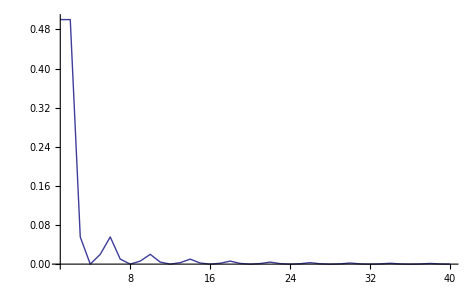

```mathematica
ListPlot[Table[allanVar[testSeqPolyACGTcomp,n]//Abs,{n,1,40}],PlotRange->All,Joined->True]
```

## Mathematica Script作成

dir:
/home/kamano/TEST_COLLECTION/AllanVarianceLike-Plot/bin/

アウトプット:
*.out.list

条件:
(window size;oligonucleotide length): 4-128;1-4(que[1]), 129-256;1-4(que[2]), 257-384;1-4(que[3]), 385-512;1-4(que[4]).